```mathematica
dimEa[a_,h_]:=If[0<=a<=1,a/h,If[1<=a<=2,Round[1/h],Round[(3-a)/h]]]
```

```mathematica
MatrixRepresentativeHt[a_,h_,t_]:=Module[{d,alpha1,alpha2,alpha4,beta,Diagonalentry,case1,case2,Xop},
d=Round[dimEa[a,h]];
alpha4[k_]:=1/h-1-k;
alpha2[k_]:=a/h-1-k;
alpha1[k_]:=3/h-alpha2[k]-2k-2;
Diagonalentry[k_]:=(1-t)h(k-alpha4[k])+8*t*h^2(k*alpha1[k]+k/2+alpha1[k]/2+1/4)-2/3*t(h(k-alpha4[k])+1/2)(2h(alpha2[k]+k+1)-3);
Xop=Module[{op},
op=Table[0,d,d];
Do[
If[m>=1,op[[m+1,m]]=-2h^2 Sqrt[(alpha1[m]+1)*(alpha2[m]+1)*(alpha4[m]+1)*(m)]];
If[m<=d-2,op[[m+1,m+2]]=-2h^2 Sqrt[alpha1[m]*alpha2[m]*alpha4[m]*(m+1)]];
,{m,0,d-1}];
op];
Table[KroneckerDelta[i,j]*Diagonalentry[i-1],{i,1,d},{j,1,d}]+(2t/3)*9/20*Xop
]
```

```mathematica
MatrixForm[MatrixRepresentativeHt[0.2,0.02,0.11]]
```

(-0.939168 | -0.00653628 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00653628 | -0.847365 | -0.00859457 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.00859457 | -0.756267 | -0.00970784 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.00970784 | -0.665872 | -0.0102296 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0102296 | -0.576181 | -0.0102884 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0102884 | -0.487195 | -0.00993089 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.00993089 | -0.398912 | -0.009149 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.009149 | -0.311333 | -0.00786277 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00786277 | -0.224459 | -0.00580434
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00580434 | -0.138288)

```mathematica
PBIϕ[F_,G_]:=D[F,o1]D[G,I1]-D[F,I1]D[G,o1]+D[F,o2]D[G,I2]-D[F,I2]D[G,o2]+D[F,o3]D[G,I3]-D[F,I3]D[G,o3]+D[F,o4]D[G,I4]-D[F,I4]D[G,o4]
```

```mathematica
Rj:=I3-I4;
N1j:=I1+I2+2*I3;
N2j:=I3+I4;
Jj=I2+I3;
Xj:=Sqrt[16I1*I2*I3*I4]*Cos[-o1-o2+o3-o4];
Yj:=Sqrt[16I1*I2*I3*I4]*Sin[-o1-o2+o3-o4];
```

```mathematica
Simplify[(N2j+Rj)/2*(N2j-Rj)/2*(Jj-(N2j+Rj)/2)*(N1j-Jj-(N2j+Rj)/2)]
```

I1 I2 I3 I4

```mathematica
Simplify[Xj^2+Yj^2]
```

16 I1 I2 I3 I4

```mathematica
rP=X^2-16*(N2+R)/2*(N2-R)/2*(J-(N2+R)/2)*(N1-J-(N2+R)/2);
```

```mathematica
Hr[s_]:=(1-s)*R+2s/3*(9/20*X-(2j-3)*(R+1/2))+8*s*I1*I3
```

```mathematica
rX=Expand[SolveValues[Hr[s]==h,X]][[1]]
```

-10/3-(80 I1 I3)/3+(20 j)/9-(10 R)/3+(40 j R)/9+(10 h)/(3 s)-(10 R)/(3 s)

```mathematica
rP11=rP/.X->rX
```

-4 (J+1/2 (-N2-R)) (-J+N1+1/2 (-N2-R)) (N2-R) (N2+R)+(-10/3-(80 I1 I3)/3+(20 j)/9-(10 R)/3+(40 j R)/9+(10 h)/(3 s)-(10 R)/(3 s))^2

```mathematica
rP1=rP11/.{I3->(N2+R)/2,I4->(N2-R)/2,I1->3-j-(N2+R)/2,I2->j-(N2+R)/2}
```

-4 (J+1/2 (-N2-R)) (-J+N1+1/2 (-N2-R)) (N2-R) (N2+R)+(-10/3+(20 j)/9-(10 R)/3+(40 j R)/9-40/3 (3-j+1/2 (-N2-R)) (N2+R)+(10 h)/(3 s)-(10 R)/(3 s))^2

```mathematica
Simplify[rP1/.{N1->3,N2->1}]
```

-((-1+2 J-R) (-1+R) (1+R) (-5+2 J+R))+(100 (3 h+(-33+14 j) s+6 R^2 s+R (-3-27 s+16 j s))^2)/(81 s^2)

```mathematica
(*Start with the bifurcation diagram*)

rDP1=FullSimplify[D[rP1,R]]
```

(2 J-N2-R) (N2-R) (N2+R)+(2 J-N2-R) (N2-R) (2 J-2 N1+N2+R)-(2 J-N2-R) (N2+R) (2 J-2 N1+N2+R)-(N2-R) (N2+R) (2 J-2 N1+N2+R)+(200 (-3+(-39+16 j+12 N2+12 R) s) (3 h-3 R+(6 (N2+R)^2+2 j (1+6 N2+8 R)-3 (1+12 N2+13 R)) s))/(81 s^2)

```mathematica
roughBD1[jv_,sv_]:=Module[{hv,Rv,p,dp,hsol},
p=(rP1/.{J->jv,j->jv,h->hv,R->Rv,N1->3,N2->1,s->sv});
dp=(rDP1/.{J->jv,j->jv,h->hv,R->Rv,N1->3,N2->1,s->sv});
hsol=NSolveValues[p==0&&dp==0&&-1<=Rv<=Min[3-jv,1],{hv,Rv}][[All,1]];
Table[{jv,hv},{hv,hsol}]
]
```

```mathematica
roughBD1[1.1,0.56]
```

{{1.1,4.93043},{1.1,-0.612844}}

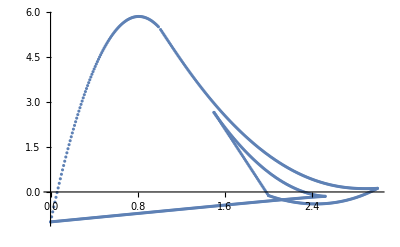

```mathematica
ListPlot[Flatten[Table[roughBD1[jv,0.56],{jv,0,3,0.01}],1]]
```

```mathematica
(*Hamiltonian flow stuff*)
```

```mathematica
Hj[s_]=(1-s)*Rj+2s/3*(9/20*Xj-(2Jj-3)(Rj+1/2))+8*s*I1*I3
```

(I3-I4) (1-s)+8 I1 I3 s+2/3 s (-((-3+2 (I2+I3)) (1/2+I3-I4))+9/5 √(I1 I2 I3 I4) Cos[o1+o2-o3+o4])

```mathematica
vfHj=Table[FullSimplify[PBIϕ[v,Hj[s]],I1>0&&I2>0&&I3>0&&I4>0],{v,{o1,o2,o3,o4,I1,I2,I3,I4}}]
```

{8 I3 s+3/5 √((I2 I3 I4)/I1) s Cos[o1+o2-o3+o4],1/15 s (-10-20 I3+20 I4+9 √((I1 I3 I4)/I2) Cos[o1+o2-o3+o4]),1+1/3 (1+24 I1-4 I2-8 I3+4 I4) s+3/5 √((I1 I2 I4)/I3) s Cos[o1+o2-o3+o4],-1-s+4/3 (I2+I3) s+3/5 √((I1 I2 I3)/I4) s Cos[o1+o2-o3+o4],6/5 √(I1 I2 I3 I4) s Sin[o1+o2-o3+o4],6/5 √(I1 I2 I3 I4) s Sin[o1+o2-o3+o4],-6/5 √(I1 I2 I3 I4) s Sin[o1+o2-o3+o4],6/5 √(I1 I2 I3 I4) s Sin[o1+o2-o3+o4]}

```mathematica
addt={o1->o1[t],o2->o2[t],o3->o3[t],o4->o4[t],I1->I1[t],I2->I2[t],I3->I3[t],I4->I4[t]};
eqsHj=MapThread[Equal,{
{o1'[t],o2'[t],o3'[t],o4'[t],I1'[t],I2'[t],I3'[t],I4'[t]},
vfHj/.addt
}]
```

{o1'[t]==8 s I3[t]+3/5 s Cos[o1[t]+o2[t]-o3[t]+o4[t]] √((I2[t] I3[t] I4[t])/I1[t]),o2'[t]==1/15 s (-10-20 I3[t]+20 I4[t]+9 Cos[o1[t]+o2[t]-o3[t]+o4[t]] √((I1[t] I3[t] I4[t])/I2[t])),o3'[t]==1+3/5 s Cos[o1[t]+o2[t]-o3[t]+o4[t]] √((I1[t] I2[t] I4[t])/I3[t])+1/3 s (1+24 I1[t]-4 I2[t]-8 I3[t]+4 I4[t]),o4'[t]==-1-s+4/3 s (I2[t]+I3[t])+3/5 s Cos[o1[t]+o2[t]-o3[t]+o4[t]] √((I1[t] I2[t] I3[t])/I4[t]),I1'[t]==6/5 s √(I1[t] I2[t] I3[t] I4[t]) Sin[o1[t]+o2[t]-o3[t]+o4[t]],I2'[t]==6/5 s √(I1[t] I2[t] I3[t] I4[t]) Sin[o1[t]+o2[t]-o3[t]+o4[t]],I3'[t]==-6/5 s √(I1[t] I2[t] I3[t] I4[t]) Sin[o1[t]+o2[t]-o3[t]+o4[t]],I4'[t]==6/5 s √(I1[t] I2[t] I3[t] I4[t]) Sin[o1[t]+o2[t]-o3[t]+o4[t]]}

```mathematica
Ydot=Simplify[PBIϕ[Yj,Hj[s]]]
```

-12/5 (I1 I2 (I3-I4)+I1 I3 I4+I2 I3 I4) s+8/3 √(I1 I2 I3 I4) (3+(3+12 I1-4 I2-16 I3) s) Cos[o1+o2-o3+o4]

```mathematica
init[jv_,hv_,N1v_,N2v_,sv_]:=Module[{Rsol,Xsol,Rv,Xv,Ydotv,o1v,o2v,o3v,o4v,I1v,I2v,I3v,I4v},
Rsol=Sort[
NSolveValues[(0==rP1/.{J->jv,j->jv,N1->N1v,N2->N2v,h->hv,s->sv,R->Rv,I3->(N2v+Rv)/2,I2->jv-(N2v+Rv)/2,I1->N1v-jv-1/2(N2v+Rv),I4->(N2v-Rv)/2})&&-1<=Rv<=Min[3-jv,1],Rv]];
DeleteMissing[Table[
Xv=(rX/.{h->hv,j->jv,R->Rv,N1->N1v,N2->N2v,s->sv,I3->(N2v+Rv)/2,I4->(N2v-Rv)/2,I1->N1v-jv-(N2v+Rv)/2});
I1v=N1v-jv-1/2*(N2v+Rv);
I2v=jv-(N2v+Rv)/2;
I3v=(N2v+Rv)/2;
I4v=(N2v-Rv)/2;
o1v=0;
o2v=0;
o3v=If[Xv>=0,0,Pi];
o4v=0;
Ydotv=(Ydot/.{I1->I1v,I2->I2v,I3->I3v,I4->I4v,o1->o1v,o2->o2v,o3->o3v,o4->o4v,s->sv});
If[Ydotv>0,{o1v,o2v,o3v,o4v,I1v,I2v,I3v,I4v},Missing[]]
,{Rv,Rsol}]]
]
```

```mathematica
init[2.1,0.1,3,1,0.67]
```

{{0,0,0,0,0.889018,2.08902,0.0109825,0.989018},{0,0,π,0,0.158822,1.35882,0.741178,0.258822}}

```mathematica
(*Other stuff*)
```

```mathematica
rP1
```

-4 (J+1/2 (-N2-R)) (-J+N1+1/2 (-N2-R)) (N2-R) (N2+R)+(-10/3+(20 j)/9-(10 R)/3+(40 j R)/9-40/3 (3-j+1/2 (-N2-R)) (N2+R)+(10 h)/(3 s)-(10 R)/(3 s))^2

```mathematica
spec[jv_,hbar_,sv_]:=Module[{hop,Rexpval,eval,evec,msize,classify,alpha4},
hop=MatrixRepresentativeHt[jv,hbar,sv];
{eval,evec}=Eigensystem[hop];
msize=Length[eval];
alpha4[k_]:=1/hbar-1-k;
Rexpval=Table[
Chop[Sum[Conjugate[evec[[i,mp1]]]*evec[[i,mp1]]*(mp1-1-alpha4[mp1-1])*hbar,{mp1,1,msize}]], 
{i,1,msize}];
classify[k_]:=Module[{Rsol,Rv},
Rsol=Sort[
NSolveValues[(0==rP1/.{J->jv,j->jv,h->eval[[k]],N1->3,N2->1,s->sv,R->Rv})&&-1<=Rv<=Min[3-jv,1],Rv]];
Which[
Length[Rsol]==2&&Rsol[[1]]<=Rexpval[[k]]<=Rsol[[2]],0,
Length[Rsol]==4&&Rsol[[1]]<=Rexpval[[k]]<=Rsol[[2]],1,
Length[Rsol]==4&&Rsol[[3]]<=Rexpval[[k]]<=Rsol[[4]],2,
Length[Rsol]==4&&Abs[Rexpval[[k]]-Rsol[[3]]]>Abs[Rexpval[[k]]-Rsol[[2]]],1,
Length[Rsol]==4&&Abs[Rexpval[[k]]-Rsol[[3]]]<Abs[Rexpval[[k]]-Rsol[[2]]],2,
True,Missing[{Length[Rsol],Rsol,Rexpval[[k]]}]]
];
Table[{N[jv],eval[[k]],classify[k]},{k,1,Length[eval]}]
]
```

```mathematica
newspec:=Flatten[Table[spec[0.015*(k+1),0.015,0.56],{k,0,198}],1]
```

```mathematica
newspec0:=Select[newspec,#[[3]]==0&][[All,{1,2}]];
```

```mathematica
newspec2:=Select[newspec,#[[3]]==2&][[All,{1,2}]];
```

```mathematica
newspec1:=Select[newspec,#[[3]]==1&][[All,{1,2}]];
```

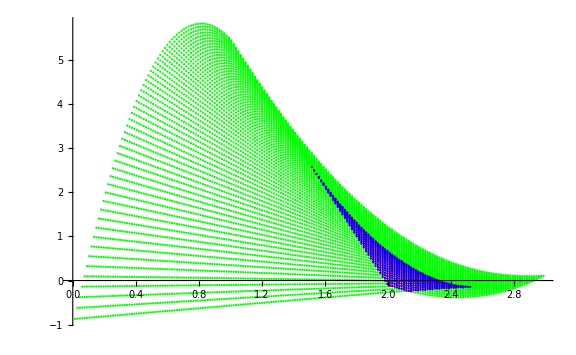

```mathematica
picspec=ListPlot[{newspec0,newspec1,newspec2},PlotStyle->{Green,Red,Blue},ImageSize->Large]
```

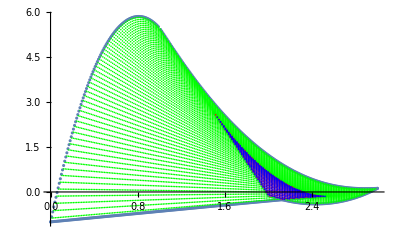

```mathematica
Show[ListPlot[Flatten[Table[roughBD1[jv,0.56],{jv,0,3,0.01}],1]],picspec]
```

```mathematica
(*Compute Action*)
```

```mathematica
computeAction[initv_,sv_]:=Module[
{act,actv,o1v,o2v,o3v,o4v,jv,N1v,N2v,T},
jv=initv[[6]]+initv[[7]];
N1v=initv[[5]]+initv[[6]]+2initv[[7]];
N2v=initv[[7]]+initv[[8]];
{actv,o1v,o2v,o3v,o4v}=NDSolveValue[{
(eqsHj/.s->sv),
MapThread[Equal,{
{o1[0],o2[0],o3[0],o4[0],I1[0],I2[0],I3[0],I4[0]},
initv
}],
{act'[t]==I1[t]*o1'[t]+I2[t]*o2'[t]+I3[t]*o3'[t]+I4[t]*o4'[t],act[0]==0},
WhenEvent[Sin[-o1[t]-o2[t]+o3[t]-o4[t]]>0,T=t;"StopIntegration"]},
{act[T],o1[T],o2[T],o3[T],o4[T]},
{t,0,Infinity}];
(actv-N1v o1v-N2v o4v-jv(o2v-o1v))/(2Pi)
]
```

```mathematica
computeAction[init[1,0.5,3,1,0.56][[1]],0.56]
```

0.113143

```mathematica
actspec0=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,0.56][[1]],0.56],jh[[2]]},{jh,newspec0}];
actspec1=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,0.56][[1]],0.56],jh[[2]]},{jh,newspec1}];
```

```mathematica
actspec2=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,0.56][[2]],0.56],jh[[2]]},{jh,newspec2}];
```

```mathematica
fixme1[{j_,a_}]:=Which[j<1,{j,a},2>j>1&&a<0,{j,1+a},j>2&&a<0,{j,3-j+a},2>j>1&&a>=0,{j,a},j>2&&a>0,{j,a}]
```

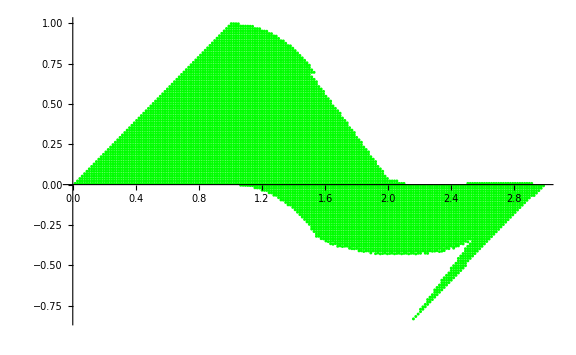

```mathematica
Show[
ListPlot[Table[{s[[1]],s[[2]]},{s,actspec0}],PlotStyle->Green,ImageSize->Large]]
```

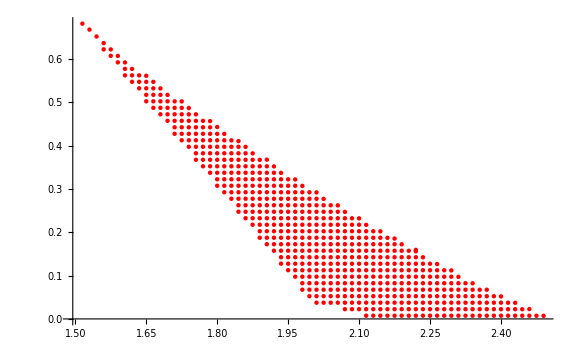

```mathematica
Show[
ListPlot[Table[{s[[1]],s[[2]]},{s,actspec1}],PlotStyle->Red,ImageSize->Large]]
```

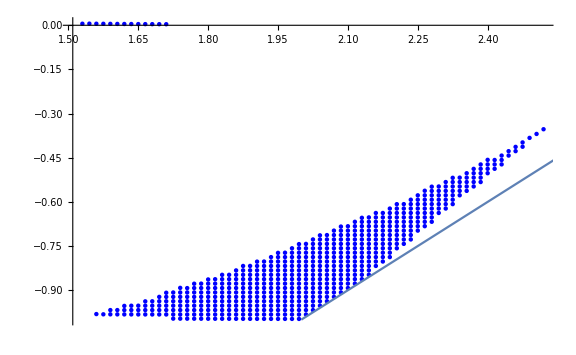

```mathematica
Show[
ListPlot[Table[{s[[1]],s[[2]]},{s,actspec2}],PlotStyle->Blue,ImageSize->Large],Plot[j-3,{j,2,3}]](*Makes sense because the points are getting "away"...*)
```

```mathematica
fixme2[{j_,a_}]:=Which[2>j>1&&a<0,{j,1+a},j>=2&&a<0,{j,(j-2)+-((j-3)-a)},2>j>1&&a>=0,{j,a},j>2&&a>0,{j,a}]
```

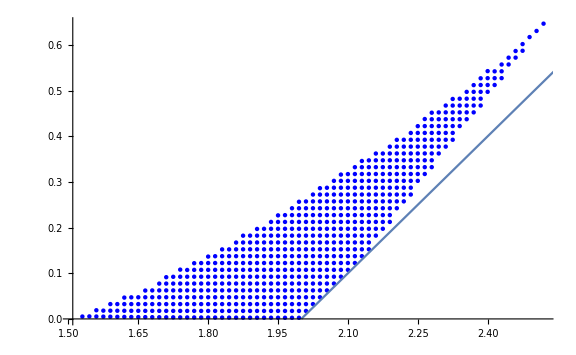

```mathematica
Show[
ListPlot[Table[fixme2[{s[[1]],s[[2]]}],{s,actspec2}],PlotStyle->Blue,ImageSize->Large],Plot[j-2,{j,2,3}]](*Makes sense because the blue points in the pleat are getting further away from the line...*)
```

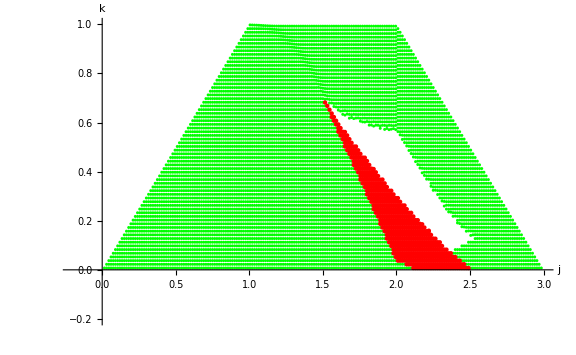

```mathematica
p1=Show[
{ListPlot[Table[fixme1[{s[[1]],s[[2]]}],{s,actspec0}],PlotStyle->Green,ImageSize->Large],ListPlot[Table[fixme1[{s[[1]],s[[2]]}],{s,actspec1}],PlotStyle->Red,ImageSize->Large]},AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1}}]
```

```mathematica
change[{j_,a_}]:=If[j<=2,{j,a},{j,j+a-2}]
```

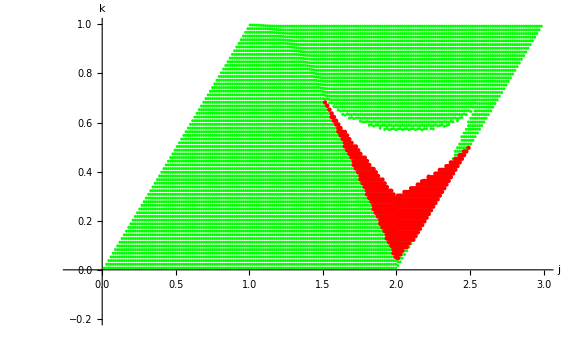

```mathematica
p2=Show[
{ListPlot[Table[change[fixme1[{s[[1]],s[[2]]}]],{s,actspec0}],PlotStyle->Green,ImageSize->Large],ListPlot[Table[change[fixme1[{s[[1]],s[[2]]}]],{s,actspec1}],PlotStyle->Red,ImageSize->Large]},AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1}}]
```

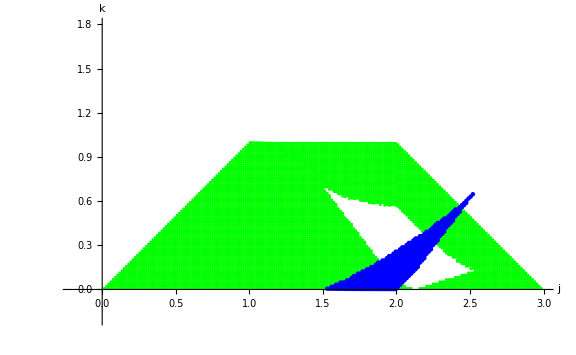

```mathematica
p3=Show[
{ListPlot[Table[fixme1[{s[[1]],s[[2]]}],{s,actspec0}],PlotStyle->Green,ImageSize->Large],ListPlot[Table[fixme2[{s[[1]],s[[2]]}],{s,actspec2}],PlotStyle->Blue,ImageSize->Large]},PlotRange->{{-.2,3},{-0.2,1.8}},AxesLabel->{j,k},ImageSize->Large]
```

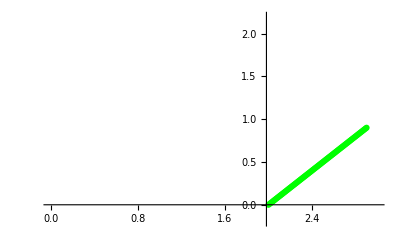

```mathematica
L1=Show[ListPlot[Table[{x,-2+x},{x,2,2.9,1/100}],PlotStyle->Green],PlotRange->{{0,3},{-0.2,2.2}}]
```

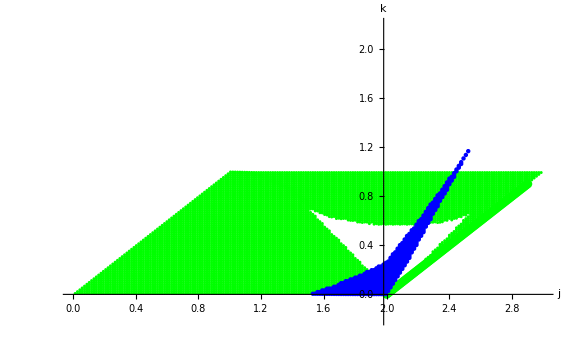

```mathematica
p4=Show[
{L1,ListPlot[Table[change[fixme1[{s[[1]],s[[2]]}]],{s,actspec0}],PlotStyle->Green,ImageSize->Large],ListPlot[Table[change[fixme2[{s[[1]],s[[2]]}]],{s,actspec2}],PlotStyle->Blue,ImageSize->Large]},PlotRange->{{0,3},{-0.2,2.2}},AxesLabel->{j,k},ImageSize->Large]
```

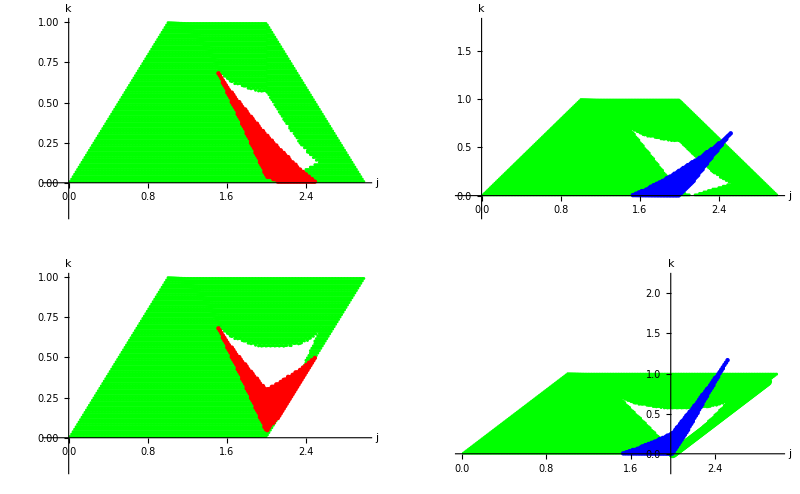

```mathematica
GraphicsGrid[{{p1,p3},{p2,p4}},Frame->All]
```